# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :1

## Práctica 4

```mathematica
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.1 *)
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.2 *)
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 4 Grafos Isomorfos - Función 5.10 *)
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   
Do[	      
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
(**)
```

```mathematica
(* Cap 5 - 2.2. Matriz de incidencia - Función 5.5 *)
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

### Ejercicio 5.29 a) Sea W el conjunto formado por todas las cifras distintas que componen su DNI junto con todas las letras distintas de su primer apellido. b) Consideramos el grafo no orientado G₁ cuyo conjunto de vértices es W y donde dos vértices cualesquiera serán adyacentes si y sólo si son: I. Un número par y una vocal. II. Un número impar y una consonante. III. Dos números pares distintos. c) Consideramos el grafo dirigido G₂ cuyo conjunto de vértices es W y donde el conjunto de flechas está formado por todas aquellas flechas que podemos considerar de la forma: I. Origen en un número impar y fin en una vocal. II. Origen en una vocal y fin en una consonante. III. Origen en un número par y fin en un número impar. Se pide:

#### I) Definir G₁ y G₂ directamente por sus conjuntos de vértices y lados o flechas.

```mathematica
W={2,6,8,0,"n","m","a","r","t","i","l","u","s"};
F1={
	{2,"a"},{2,"i"},{2,"u"},{6,"a"},{6,"i"},{6,"u"},{8,"a"},{8,"i"},{8,"u"},
	{0,"n"},{0,"m"},{0,"r"},{0,"t"},{0,"l"},{0,"s"},
	{2,6},{2,8},{6,8}
};
F2={
	{0,"a"},{0,"i"},{0,"u"},
	{"a","n"},{"a","m"},{"a","r"},{"a","t"},{"a","l"},{"a","s"},
	{"i","n"},{"i","m"},{"i","r"},{"i","t"},{"i","l"},{"i","s"},
	{"u","n"},{"u","m"},{"u","r"},{"u","t"},{"u","l"},{"u","s"},
	{2,0},{6,0},{8,0}
};
```

#### II) Calcular las matrices de adyacencia de G₁ y G₂.

```mathematica
A1=MATRIZADYACENCIA[W,F1];
A1//MatrixForm
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
A2=MATRIZADYACENCIADIR[W,F2];
A2//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### III) Calcular la matriz de incidencia de G₁.

```mathematica
M1=MATRIZINCIDENCIA[W,F1];
M1//MatrixForm
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

#### IV) Representar gráficamente G₁ y G₂.

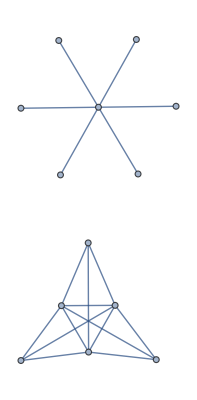

```mathematica
GraphPlot[A1]
```

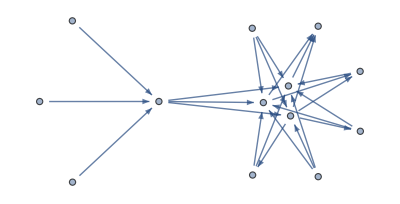

```mathematica
GraphPlot[A2,EdgeRenderingFunction->({Arrow[#1,0.1]}&)]
```

### Ejercicio 2 Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

#### a) -Graphics-

```mathematica
WEjer2GIa={1,2,3,4,5,6};
FEjer2GIa={1->2,3->1,4->5,6->1}

"MATRIZADYACENCIA"
AEjer2GIa=MATRIZADYACENCIA[WEjer2GIa,FEjer2GIa];
AEjer2GIa//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIa=MATRIZINCIDENCIA[WEjer2GIa,FEjer2GIa];
IEjer2GIa//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIa;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIa,DirectedEdges->True]
```

{1→2,3→1,4→5,6→1}

MATRIZADYACENCIA

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

MATRIZINCIDENCIA

(1 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6}

{2→1,3→1,6→1,1→2,1→3,5→4,4→5,1→6}

Representacion gráfica

-Graphics-

#### b)-Graphics-

```mathematica
matrizadyacenciaEjer2GIb=({{0, 1, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}});
Wb=Table[i,{i,Dimensions[matrizadyacenciaEjer2GIb]⟦1⟧}]
Fb={};
Do[Do[If[matrizadyacenciaEjer2GIb⟦i,j⟧==1,AppendTo[Fb,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacenciaEjer2GIb]⟦1⟧}];
Fb
```

{1,2,3,4}

{1→2,2→3,1→4,3→4}

```mathematica
WEjer2GIb={1,2,3,4};
FEjer2GIb={1->2,2->3,1->4,3->4};
"MATRIZINCIDENCIA"
IEjer2GIb=MATRIZINCIDENCIA[WEjer2GIb,FEjer2GIb];
IEjer2GIb//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}]
F={};
Do[Do[If[matrizadyacenciaEjer2GIb[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];,{j,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];
F
"Representacion gráfica"
GraphPlot[matrizadyacenciaEjer2GIb,DirectedEdges->True]
```

MATRIZINCIDENCIA

(1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1)

Vertices y lados

{1,2,3,4}

{2→1,4→1,1→2,3→2,2→3,4→3,1→4,3→4}

Representacion gráfica

-Graphics-

#### c)-Graphics-

```mathematica
matrizincidenciaEjer2GIc=({{1, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}});

W=Table[i,{i,Dimensions[matrizincidenciaEjer2GIc][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer2GIc][[2]]}];
F
```

{1,2,3,4,5}

{1→4,1→5,2→4,2→5,3→4,3→5}

```mathematica
WEjer2GIc={1,2,3,4,5};
FEjer2GIc={1->4,1->5,2->4,2->5,3->4,3->5};
"MATRIZADYACENCIA"
AEjer2GIc=MATRIZADYACENCIA[WEjer2GIc,FEjer2GIc];
AEjer2GIc//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[AEjer2GIc][[1]]}]
F={};
Do[Do[If[AEjer2GIc[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[AEjer2GIc][[1]]}];,{j,Dimensions[AEjer2GIc][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIc,DirectedEdges->True]
```

MATRIZADYACENCIA

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

Vertices y lados

{1,2,3,4,5}

{4→1,5→1,4→2,5→2,4→3,5→3,1→4,2→4,3→4,1→5,2→5,3→5}

Representacion gráfica

-Graphics-

#### d)-Graphics-

```mathematica
"d"
WEjer2GIdg4={1,2,3,4,5,6,7,8};
FEjer2GIdg4={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8}
"MATRIZADYACENCIA"
AEjer2GIdg4=MATRIZADYACENCIA[WEjer2GIdg4,FEjer2GIdg4];
AEjer2GIdg4//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg4=MATRIZINCIDENCIA[WEjer2GIdg4,FEjer2GIdg4];
IEjer2GIdg4//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIdg4;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIdg4,DirectedEdges->True]
```

d

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→1,1→4,2→7,3→6,5→8}

MATRIZADYACENCIA

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

MATRIZINCIDENCIA

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6,7,8}

{2→1,4→1,8→1,1→2,3→2,7→2,2→3,4→3,6→3,1→4,3→4,5→4,4→5,6→5,8→5,3→6,5→6,7→6,2→7,6→7,8→7,1→8,5→8,7→8}

Representacion gráfica

-Graphics-

### Ejercicio 3 Ejercicio 5.4 del manual de prácticas Estudiar si son isomorfos los siguientes grafos

#### a) -Graphics-

```mathematica
WEjer3GIdgb={1,2,3,4,5,6};
FEjer3GIdgb={{1,2},{2,3},{3,6},{6,5},{5,4},{4,1}};
AGa=MATRIZADYACENCIA[WEjer3GIdgb,FEjer3GIdgb];
MatrixForm[AGa]
```

(0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0)

#### b) -Graphics-

```mathematica
AGb=({{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0}});
MatrixForm[AGb]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0)

#### c) -Graphics-

```mathematica
WEjer3GIdgc={1,2,3,4,5,6};
FEjer3GIdgc={{1,6},{1,5},{2,4},{2,6},{3,4},{3,5}};
AGc=MATRIZADYACENCIA[WEjer3GIdgc,FEjer3GIdgc];
MatrixForm[AGc]
```

(0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0)

#### d) -Graphics-

```mathematica
AGd=({{0, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 1, 0, 0, 1, 0}});
MatrixForm[AGd]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1 | 0)

#### e) -Graphics-

```mathematica
matrizincidenciaEjer3GIe=({{1, 0, 0, 1, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 1, 0, 0, 1}, {0, 1, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 1}});


W=Table[i,{i,Dimensions[matrizincidenciaEjer3GIe][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer3GIe][[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer3GIe][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer3GIe][[2]]}];
F
```

{1,2,3,4,5,6}

{1→6,2→5,3→4,1→2,3→5,4→6}

```mathematica
WEjer3GIdge={1,2,3,4,5,6};
FEjer3GIdge={1->6,2->5,3->4,1->2,3->5,4->6};
AGe=MATRIZADYACENCIA[WEjer3GIdge,FEjer3GIdge];
MatrixForm[AGe]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0)

#### f) -Graphics-

```mathematica
WEjer3GIdgf={1,2,3,4,5,6};
FEjer3GIdgf={1->2, 1->3, 2->3, 3->5, 4->5,4->6, 5->6};
AGf=MATRIZADYACENCIA[WEjer3GIdgf,FEjer3GIdgf];
MatrixForm[AGf]
```

(0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0)

```mathematica
"Ga y Gb"
ISOMORFOS[AGa,AGb]
"Ga y Gc"
ISOMORFOS[AGa,AGc]
"Ga y Gd"
ISOMORFOS[AGa,AGd]
"Ga y Ge"
ISOMORFOS[AGa,AGe]
"Ga y Gf"
ISOMORFOS[AGa,AGf]
"Gb y Gc"
ISOMORFOS[AGb,AGc]
"Gb y Gd"
ISOMORFOS[AGb,AGd]
"Gb y Ge"
ISOMORFOS[AGb,AGe]
"Gb y Gf"
ISOMORFOS[AGb,AGf]
"Gc y Gd"
ISOMORFOS[AGc,AGd]
"Gc y Ge"
ISOMORFOS[AGc,AGe]
"Gc y Gf"
ISOMORFOS[AGc,AGf]
"Gd y Ge"
ISOMORFOS[AGd,AGe]
"Gd y Gf"
ISOMORFOS[AGd,AGf]
"Ge y Gf"
ISOMORFOS[AGe,AGf]
```

Ga y Gb

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 6 | 5 | 4)

Ga y Gc

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 6 | 4 | 2)

Ga y Gd

No son isomorfos

Ga y Ge

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 6 | 5 | 3 | 4)

Ga y Gf

No son isomorfos

Gb y Gc

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 4 | 6 | 2)

Gb y Gd

No son isomorfos

Gb y Ge

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 4 | 5 | 3 | 6)

Gb y Gf

No son isomorfos

Gc y Gd

No son isomorfos

Gc y Ge

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 5 | 4 | 2 | 3 | 6)

Gc y Gf

No son isomorfos

Gd y Ge

No son isomorfos

Gd y Gf

No son isomorfos

Ge y Gf

No son isomorfos